```mathematica
Answers to Exercises   Huanjie Guo    ID：10655496
```

```mathematica
Week 3
```

Q1 two worked examples of Euler’s Theorem including all the details (i.e. m, a, EulerPhi[m], PowerMod[a,EulerPhi[m],m]) — one where the numbers are fairly small and one where the numbers are bigger;

# small number
m=5;a=12;
EulerPhi[m]
4
PowerMod[a,EulerPhi[m],m]
1

# bigger number
m=11010111211;a=10000079;
EulerPhi[m]
10002455040
PowerMod[a,EulerPhi[m],m]
1

Q2 an example of the working of ExtendedGCD, showing that recombining the multipliers with the two original numbers yields the GCD;
# (-9)*121+5*220 = 11
ExtendedGCD[121,220]
{11,{-9,5}}

Q3 an example of the working of ChineseRemainder using moduli 13, 29, 64, determining u1, u2, u3,and checking that ChineseRemainder acting on {10,5,7} yields the same as 10u1 +  5u2 +7u3 mod 13 *29 *64;
# calculate u1
ChineseRemainder[{1,0,0},{13,29,64}]
7424
# calculate u2
ChineseRemainder[{0,1,0},{13,29,64}]
13312
# calculate u3
ChineseRemainder[{0,0,1},{13,29,64}]
3393

ChineseRemainder[{10,5,7},{13,29,64}]
19783
10u1 +  5u2 + 7u3 mod 13 * 29 * 64 = 19783

Q4 the details of your Diffie-Hellman key exchange example;
# choose p
p = Prime[1000001]
15485867

# choose a
a = 2

# Alice chooses as a random secret exponent m_A=69 and Bob as a random secret exponent m_B=103
ma = 69
mb = 103

# get cA and cB
cA=PowerMod[a,ma,p]
14482528
cB=PowerMod[a,mb,p]
14277311

# Alice can compute the common key with Bob by raising the publicly known c_B to the power m_A, which she only knows. She gets:
PowerMod[cB,ma,p]
14224808

 # Bob gets the same common key by raising c_A to the power m_B. Indeed, he gets:
 PowerMod[cA,mb,p]
14224808

Q5 the details of your ElGamal public key cryptosystem example;

# Alice choose q and a
q = Prime[1000003]
15485927
a= 2
2

# Alice choose Private key and generate Public key
PrivateA = RandomInteger[{0,q-1}]
8579339
PublicA = PowerMod[a,PrivateA,q]
4099103

# Bob get PU = {q=15485927,a=2,PublicA = 4099103}
# choose plaintext 5880
M = 5880
5880
k = RandomInteger[{0,q-1}]
4143699

# Bob generator one-time key K 
K = PowerMod[PublicA,k,q]
6629221

# Bob generate C1 and C2
C1 = PowerMod[a,k,q]
8496381
C2 = Mod[K*M,q]
1741221

# Alice receive C1 and C2, use her Private Key to decrypt.
NewK = PowerMod[C1,PrivateA,q]
6629221
M = Mod[C2*PowerMod[NewK,-1,q],q]
5880

Q6 the details of your ElGamal public key signature example;
# Alice generate S1 and S2
q=Prime[1000003]
15485927
PrimitiveRootList[q]
{5,7,10,13,14,15,20,21,23,26,29,30,31,39,40,41,42,43,45,46,52,55,56,58,60,61,7415948,15485877,15485878,15485880,15485883,15485889,15485890,15485891,15485892,15485894,15485895,15485900,15485902,15485903,15485905,15485908,15485909,15485910,15485911,15485915,15485916,15485918,15485919,15485921,15485923,15485924,15485925}
 |  |  |  | 
a=5
5
PrivateA=RandomInteger[{0,q-1}]
8346382
PublicA=PowerMod[a,PrivateA,q]
3551317
M=5880
5880
k=RandomInteger[{0,q-1}]
3312473
S1=PowerMod[a,k,q]
9830973
K=PowerMod[k,-1,q-1]
6904381
S2=Mod[K*Mod[M-PrivateA*S1,q-1],q-1]
11346278

# Bob compare v1 and v2, if  v1==v2, the message is valid.
v1=PowerMod[a,M,q]
5420128
v2=Mod[Power[PublicA,S1]*Power[S1,S2],q]
5420128

Q7 the details of RSA encryption and decryption starting from your own primes;
# get nB
pB=Prime[1000005]
qB = Prime[1000018]
nB=pB*qB
phiB = (pB-1)*(qB-1)
15485941
15486181
239818085281321
239818054309200

# get eB,dB, eB*dB = 1 mod nB
eB=RandomInteger[{1,nB}];
While[GCD[eB,phiB]≠1,eB=RandomInteger[{1,nB}]];
eB
ExtendedGCD[eB,phiB]

32554268125351
{1,{90641561823751,-12304201680773}}

dB=90641561823751;

# encryption
m = 5880361;
c=PowerMod[m,eB,nB]
179362002275282

# decryption
PowerMod[c,dB,nB]
5880361

Q8 the details of securely encrypting and signing a message from Alice to Bob, including the verification at Bob’s end.
# get Alice’s Public Key and Private Key
pA=Prime[10000131]
qA = Prime[10023112]
nA=pA*qA
phiA = (pA-1)*(qA-1)
179427161
179861443
32272028090853323
32272027731564720
eA=RandomInteger[{1,nA}];
While[GCD[eA,phiA]≠1,eA=RandomInteger[{1,nA}]];
eA
ExtendedGCD[eA,phiA]
25767449002289833
{1,{-9096513544648823,7263068525164923}}
dA = -9096513544648823
-9096513544648823

# get Bob Public Key and Private Key
pB=Prime[1000005]
qB = Prime[1000018]
nB=pB*qB
phiB = (pB-1)*(qB-1)
15485941
15486181
239818085281321
239818054309200
eB=RandomInteger[{1,nB}];
While[GCD[eB,phiB]≠1,eB=RandomInteger[{1,nB}]];
eB
ExtendedGCD[eB,phiB]
104061532455479
{1,{107216632275719,-46523299054632}}
dB = 107216632275719
107216632275719

# Alice want to send “5880361”
# she uses Bob’s public key to generate ciphertext c
# she uses her private key to genenrate signature 
mA = 5880361;
c = PowerMod[mA,eB,nB]
203592072207584
signature = PowerMod[c,dA,nA]
21071830361918155

# Bob receives c and signature of c
# Bob uses Alice’s Public Key to check if the ciphertext was sent from Alice, and he finds that checkSign == c
checkSign = PowerMod[signature,eA,nA]
203592072207584
# After check the signature, Bob uses his Private Key to decrypt the ciphertext and get the message mA
receiveMA = PowerMod[c,dB,nB]
5880361

```mathematica
Week 4
```

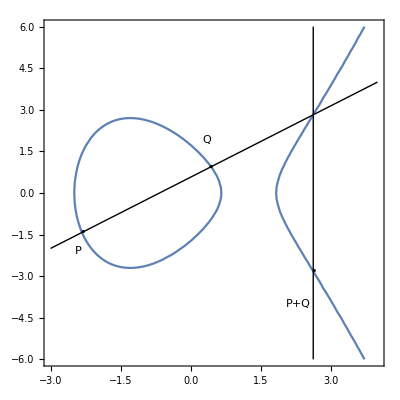
Q1 the ContourPlot and its output for the y2 =x3 - 5x + 3 elliptic curve example from Section 10.2, including the Epilog->Line, as the coefficient of x varies from -5 to -3;

Manipulate[ContourPlot[y^2== x^3+n x+3,{x,-3,3},{y,-4,4},Axes→True,Epilog→Line[{{-3,4},{4,-3}}]],{n,-5,-3}]


Q2 an answer to the question about straight lines intersecting elliptic curves in three places;

When the coefficient of x is -3, it only have one intersection.
NSolve[ {y^2==x^3-3 x+3,y==-x+1},{x,y}]
{{x→-1.20557,y→2.20557},{x→1.10278+0.665457 ⅈ,y→-0.102785-0.665457 ⅈ},{x→1.10278-0.665457 ⅈ,y→-0.102785+0.665457 ⅈ}}

Q3 the ContourPlot and its output for the example of addition of two points on a curve over the reals, where the first line is given by {{-3,-2},{4,4}} and including the bullet that represents the answer; 

NSolve[ {y^2==x^3-5 x+3,7y==6x+4},{x,y}]
{{x→2.62478,y→2.82124},{x→-2.32767,y→-1.42371},{x→0.437585,y→0.946501}}

ContourPlot[ y^2 ==x^3-5 x+ 3,{x,-3,4},{y,-6,6},Axes→True,	Epilog->{Line[{{-3,-2},{4,4}}],Line[{{2.6247755634983756,-6},{2.6247755634983756,6}}],Text["P+Q",{2.3,-4}],			Text["P",{-2.4,-2.1}],			Text["Q",{0.35,1.9}],			Text["•",{-2.31,-1.4}],			Text["•",{0.43758485089023075,0.9465013007630549}],			Text["•",{2.6247755634983756,-2.821236197284322}]}]
-Graphics-

Q4 the Table example (without the enclosing Flatten) that runs through the points of the y2 = x3  - 5x + 3
elliptic curve over Z11;

Clear[x,y]; 
p=11;
Table[ Solve[ {y^2== x^3-5 x + 3, x==u},{x,y}, Modulus->p], {u, 0, p-1}]
{{{x→0,y→5},{x→0,y→6}},{},{{x→2,y→1},{x→2,y→10}},{{x→3,y→2},{x→3,y→9}},{{x→4,y→5},{x→4,y→6}},{{x→5,y→2},{x→5,y→9}},{},{{x→7,y→5},{x→7,y→6}},{},{{x→9,y→4},{x→9,y→7}},{}}


Q5 the Solve example that finds the points of intersection of the straight line you chose with the
y2 = x3  - 5x + 3 elliptic curve over Z11;

# we choose (0,5) and (4,6) and get its  formula. y = 5+x/4
InterpolatingPolynomial[{{0,5},{4,6}},t]
5+t/4

# calculate intersection
p=11;Solve[ {y^2==x^3-5 x+3,y==5+x/4},{x,y},Modulus-> p]
{{x→0,y→5},{x→4,y→6},{x→5,y→9}}

Q6 the result of EllipticAdd with the curve y2 = x3 - 5x + 3 and the points defining the straight line you chose for the previous question, and the relationship between the answer here and the previous answer; 

# we choose {0,5} , {4,6} ,which is on the same line with {5,9}, and we add the first two point and get the result which is  {5,2}.
p=11;a=0;b=-5;c=3;EllipticAdd[p,a,b,c,{0,5},{4,6}]
{5,2}
#   The third point is {5,9}. we can find that actually y = -(9) mod 11 = 2 and x is the same as  Q.x  which is 5.

 Q7 the Table containing the first 10-20 doublings of {121,517}, the IntegerDigits of 432, and the confirmation that the relevant combination of these via EllipticAdd yields the point at infinity;

Table[P[n],{n,1,10,1}]
{{630,588},{447,354},{69,852},{348,843},{539,467},{572,822},{124,198},{804,143},{363,372},{533,612}}

IntegerDigits[432,2]
{1,1,0,1,1,0,0,0,0}

#   calculate p[8]+p[7]+p[5]+p[4]  = {0} , and the order of {121,517} is 432.
EllipticAdd[p,a,b,c,EllipticAdd[p,a,b,c,{804,143}，{124,198}],		 EllipticAdd[p,a,b,c,{539,467},{348,843}]]
{O}

Q8 the details of the Diffie-Hellman protocol starting from the primitive element that you chose, including: proving that the point lies on the curve y2 = x3 + 100x2 + 10x + 1 over Z863, deriving QAlice, QBob, QA, QB, as in the example, confirming that QA and QB are equal;

# choose {48,357} , and check if it lies on the curve
p=863;a=100;b=10;c=1;x=48;y=357;Mod[y^2-(x^3+a*x^2+b*x+c),p]==0
True

# check {48,357} order is bigger than 10
P = {48,357}
f[1] = P;
f[n_]:= f[n] = EllipticAdd[p,a,b,c,P,f[n-1]]
Column[Table[f[n],{n,1,10,1}]]
{48,357}
{84,681}
{712,571}
{38,608}
{211,196}
{471,262}
{566,453}
{128,78}
{787,203}
{51,377}

# let Alice choose mA = 11, mB = 20 Then QAlice = {112,82}, QBob = {792,644}
QAlice=EllipticAdd[p,a,b,c,P[3],P[1]]
QBob=EllipticAdd[p,a,b,c,P[4],P[2]]
{112,82}
{792,644}

# Alice can Compute the common key K.(A,B) with the calculation K.(A,B) = (m.A)*Q.B, where m.A is the 11
QA[0]={792,644};QA[i_]:=QA[i]=EllipticAdd[p,a,b,c,QA[i-1],QA[i-1]];EllipticAdd[p,a,b,c,QA[3],QA[1]]
{548,440}

# Bob can Compute the common key K.(A,B) with the calculation K.(A,B) = (m.B)*Q.A, where m.b is the 20
QB[0]={112,82};QB[i_]:=QB[i]=EllipticAdd[p,a,b,c,QB[i-1],QB[i-1]];EllipticAdd[p,a,b,c,QB[4],QB[2]]
{548,440}

Q9 the preliminary calculations with finite fields of characteristic 2 with non-trivial extension degree, including the basic manipulations with dd and ee, and including the tabulation of powers of dd;

<<FiniteFields`

z16=GF[2,4]
GF[2,{1,0,0,1,1}]
dd=z16[{0,0,1,1}]
{0,0,1,1}_2
dd+dd
0
dd-dd
0
ee=z16[{1,1,0,0}]
{1,1,0,0}_2
dd ee
{1,0,1,1}_2
dd/ee
{0,0,1,0}_2

Table[dd^n,{n,0,15,1}]
{1,{0,0,1,1}_2,{0,1,1,0}_2,{1,1,0,0}_2,{1,0,1,1}_2,{0,1,0,1}_2,{1,0,1,0}_2,{0,1,1,1}_2,{1,1,1,0}_2,{1,1,1,1}_2,{1,1,0,1}_2,{1,0,0,1}_2,{0,0,0,1}_2,{0,0,1,0}_2,{0,1,0,0}_2,{1,0,0,0}_2}

Table[dd^n,{n,0,30,1}]
{1,{0,0,1,1}_2,{0,1,1,0}_2,{1,1,0,0}_2,{1,0,1,1}_2,{0,1,0,1}_2,{1,0,1,0}_2,{0,1,1,1}_2,{1,1,1,0}_2,{1,1,1,1}_2,{1,1,0,1}_2,{1,0,0,1}_2,{0,0,0,1}_2,{0,0,1,0}_2,{0,1,0,0}_2,{1,0,0,0}_2,{0,0,1,1}_2,{0,1,1,0}_2,{1,1,0,0}_2,{1,0,1,1}_2,{0,1,0,1}_2,{1,0,1,0}_2,{0,1,1,1}_2,{1,1,1,0}_2,{1,1,1,1}_2,{1,1,0,1}_2,{1,0,0,1}_2,{0,0,0,1}_2,{0,0,1,0}_2,{0,1,0,0}_2,{1,0,0,0}_2}


Q10 the derivation of the solution of y2 + xy = x3 + a x2 + c for the given parameters, and including the tabulation of PDoubles;

Column[Table[(dd^n)^3+ee(dd^n)^2,{n,0,15,1}]]
{0,1,0,0}_2
{1,0,0,1}_2
{1,1,0,1}_2
0
{1,0,0,0}_2
{1,0,1,0}_2
{0,1,0,0}_2
{1,1,0,0}_2
{0,1,0,0}_2
{1,0,1,1}_2
{0,1,1,0}_2
{0,0,0,1}_2
{1,0,1,1}_2
{1,0,1,1}_2
{0,0,1,0}_2
{0,1,0,0}_2

# we can find that when n = 3, we get zero. so n=3
x = y = dd^3;
y^2+x y
0
x^3+ee x^2
0

P=.;
a=ee;c=0;
P[0]={dd^3,dd^3};
P[i_]:=P[i]=Z2mEllipticAdd[a,c,P[i-1],P[i-1]]

PDouble = Column[Table[P[n],{n,0,31,1}]]
{{1,1,0,0}_2,{1,1,0,0}_2}
{{1,0,1,0}_2,{0,1,0,1}_2}
{{0,0,0,1}_2,{0,1,0,1}_2}
{{1,1,1,1}_2,{1,1,0,0}_2}
{{1,1,0,0}_2,0}
{{1,0,1,0}_2,{1,1,1,1}_2}
{{0,0,0,1}_2,{0,1,0,0}_2}
{{1,1,1,1}_2,{0,0,1,1}_2}
{{1,1,0,0}_2,{1,1,0,0}_2}
{{1,0,1,0}_2,{0,1,0,1}_2}
{{0,0,0,1}_2,{0,1,0,1}_2}
{{1,1,1,1}_2,{1,1,0,0}_2}
{{1,1,0,0}_2,0}
{{1,0,1,0}_2,{1,1,1,1}_2}
{{0,0,0,1}_2,{0,1,0,0}_2}
{{1,1,1,1}_2,{0,0,1,1}_2}
{{1,1,0,0}_2,{1,1,0,0}_2}
{{1,0,1,0}_2,{0,1,0,1}_2}
{{0,0,0,1}_2,{0,1,0,1}_2}
{{1,1,1,1}_2,{1,1,0,0}_2}
{{1,1,0,0}_2,0}
{{1,0,1,0}_2,{1,1,1,1}_2}
{{0,0,0,1}_2,{0,1,0,0}_2}
{{1,1,1,1}_2,{0,0,1,1}_2}
{{1,1,0,0}_2,{1,1,0,0}_2}
{{1,0,1,0}_2,{0,1,0,1}_2}
{{0,0,0,1}_2,{0,1,0,1}_2}
{{1,1,1,1}_2,{1,1,0,0}_2}
{{1,1,0,0}_2,0}
{{1,0,1,0}_2,{1,1,1,1}_2}
{{0,0,0,1}_2,{0,1,0,0}_2}
{{1,1,1,1}_2,{0,0,1,1}_2}

Q11 the derivation of the Diffie-Hellman protocol for the case cited.

# Alice choose mA = 11, Bob choose mB = 20

# Alice and bob generate their point and then sent it to each other
QAlice = Z2mEllipticAdd[a,c,PDouble[[3]],PDouble[[1]]]
{{0,1,0,0}_2,{1,0,1,1}_2}
QBob = Z2mEllipticAdd[a,c,PDouble[[4]],PDouble[[2]]]
{{0,0,1,0}_2,{1,1,0,1}_2}

# Alice use bob’s point and her key mA = 11 to calculate
QAB = .;QAB[0] = QBob;
QAB[i_] := QAB[i] = Z2mEllipticAdd[a,c,QAB[i-1],QAB[i-1]];
Z2mEllipticAdd[a,c,QAB[3],QAB[1]]
{{1,0,1,0}_2,{1,1,1,1}_2}

# Bob use Alice point and his key mB=20 to calculate
QBA = .;QBA[0] = QAlice;
QBA[i_] := QBA[i] = Z2mEllipticAdd[a,c,QBA[i-1],QBA[i-1]];
Z2mEllipticAdd[a,c,QBA[4],QBA[2]]
{{1,0,1,0}_2,{1,1,1,1}_2}

```mathematica
Week 5
```

Q1 the programs and outputs produced for your simulation of the BB84 QKD protocol, namely: AliceBasis AliceData, BobBasis, BobData, EqualBases, AgreedDataAlice, AgreedDataBob, (the code that produces, and the values of) AgreedKeyAlice, AgreedDataBob, CheckDigitsAlice, CheckDigitsBob ;

# generate Alice Data and the direction of data
AliceBasis = Table[RandomInteger[1],{n,1,40,1}]
{0,1,1,0,0,0,0,0,1,0,0,1,1,0,0,1,1,0,1,0,1,1,1,1,0,0,0,0,1,0,0,0,1,1,1,0,1,1,1,0}
AliceData = Table[RandomInteger[1],{n,1,40,1}]
{1,0,0,0,1,0,1,0,0,1,0,1,0,0,0,1,0,1,0,1,0,1,1,0,0,1,0,1,1,1,0,0,0,1,1,1,1,1,1,0}

# Bob generate his direction and tell Alice
BobBasis = Table[RandomInteger[1],{n,1,40,1}]
{0,0,1,0,0,1,0,0,0,0,1,0,0,0,0,0,1,1,0,1,1,1,1,0,1,0,0,0,0,0,0,1,1,0,1,0,0,0,0,1}

# Bob put the bit when direction of Alice and bob are the same. Otherwise she use random number.
BobData = Table[If[AliceBasis[[n]]==BobBasis[[n]],AliceData[[n]],RandomInteger[1]],{n,1,40,1}]
{1,0,0,0,1,1,1,0,0,1,1,1,1,0,0,0,0,0,1,1,0,1,1,0,1,1,0,1,1,1,0,1,0,0,1,1,0,1,0,0}

# a table to tell which bit of two direction is the same.
EqualBases = Table[If[AliceBasis[[n]]==BobBasis[[n]],1,0],{n,1,40,1}]
{1,0,1,1,1,0,1,1,0,1,0,0,0,1,1,0,1,0,0,0,1,1,1,0,0,1,1,1,0,1,1,0,1,0,1,1,0,0,0,0}

AgreedDataAlice = {};
AgreedDataBob = {};

# Alice generate her data
For[n=1,n<41,n++,If[EqualBases[[n]]==1,AgreedDataAlice = Append[AgreedDataAlice,AliceData[[n]]]]]
AgreedDataAlice
{1,0,0,1,1,0,1,0,0,0,0,1,1,1,0,1,1,0,0,1,1}

# Bob get his data
For[n=1,n<41,n++,If[EqualBases[[n]]==1,AgreedDataBob = Append[AgreedDataBob,BobData[[n]]]]]
AgreedDataBob
{1,0,0,1,1,0,1,0,0,0,0,1,1,1,0,1,1,0,0,1,1}

AgreedKeyAlice = {};
AgreedKeyBob = {};
CheckDigitsAlice = {};
CheckDightsBob = {};

# we split data randomly
For[i=1,i<=Length[AgreedDataAlice],i++,
If[
 RandomInteger[1]== 1
,{AgreedKeyAlice = Append[AgreedKeyAlice,AgreedDataAlice[[i]]],AgreedKeyBob = Append[AgreedKeyBob,AgreedDataBob[[i]]]}
,{CheckDigitsAlice = Append[CheckDigitsAlice,AgreedDataAlice[[i]]],CheckDightsBob = Append[CheckDightsBob,AgreedDataBob[[i]]]}
]
]
AgreedKeyAlice
{0,1,1,0,0,1,1,0,1}
AgreedKeyBob
{0,1,1,0,0,1,1,0,1}
CheckDigitsAlice
{1,0,0,1,0,0,1,0,1,1,0,1}
CheckDightsBob
{1,0,0,1,0,0,1,0,1,1,0,1}

Q2 the programs and outputs produced for your simulation of the B 92 QKD protocol, namely: AliceData, AliceBasis, BobBasis, BobData, AgreedDataAlice, AgreedDataBob, (code etc., needed for) AgreedKeyAlice, AgreedKeyBob, CheckDigitsAlice, CheckDigitsBob ;

len = 40
40
AliceBasis = Table[RandomInteger[1],{,1,len,1}]
{0,0,1,1,1,0,0,1,0,1,1,0,0,0,0,1,1,0,1,0,0,0,0,1,1,1,1,0,1,1,0,0,0,1,1,0,0,1,1,1}
AliceData = AliceBasis
{0,0,1,1,1,0,0,1,0,1,1,0,0,0,0,1,1,0,1,0,0,0,0,1,1,1,1,0,1,1,0,0,0,1,1,0,0,1,1,1}
BobBasis = Table[RandomInteger[1],{,1,len,1}]
{1,1,0,0,1,0,0,1,0,1,0,0,1,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0}

# Bob put the bit when direction of Alice and bob are the same. Otherwise she use random number.
BobData = Table[If[AliceBasis[[i]]==BobBasis[[i]],AliceData[[i]],RandomInteger[1]],{i,1,len,1}]
{0,0,1,0,1,0,0,1,0,1,1,0,0,0,0,0,1,0,1,0,1,1,1,1,1,1,1,0,1,1,1,0,0,1,1,0,0,0,1,1}

# reliable data when BobBasis ≠ BobData

ReliableData = Table[If[BobBasis[[n]]≠ BobData[[n]],1,0],{n,1,len,1}]
{1,1,1,0,0,0,0,0,0,0,1,0,1,0,0,0,1,1,0,1,0,0,0,1,1,1,1,0,1,1,0,0,0,1,0,0,0,0,0,1}

AgreedDataAlice={};
AgreedDataBob = {};

For[ i=1,i<= Length[ReliableData],i++ , If[ReliableData[[i]]==1,
{AgreedDataAlice = Append[AgreedDataAlice,AliceData[[i]]];
AgreedDataBob = Append[AgreedDataBob,BobData[[i]]];
}]]

AgreedDataAlice
{0,0,1,1,0,1,0,0,1,1,1,1,1,1,1,1}
AgreedDataBob
{0,0,1,1,0,1,0,0,1,1,1,1,1,1,1,1}

AgreedKeyAlice = {};
AgreedKeyBob = {};
CheckDigitsAlice = {};
CheckDightsBob = {};

# we split data randomly
For[i=1,i<=Length[AgreedDataAlice],i++,
If[
 RandomInteger[1]== 1
,{AgreedKeyAlice = Append[AgreedKeyAlice,AgreedDataAlice[[i]]],AgreedKeyBob = Append[AgreedKeyBob,AgreedDataBob[[i]]]}
,{CheckDigitsAlice = Append[CheckDigitsAlice,AgreedDataAlice[[i]]],CheckDightsBob = Append[CheckDightsBob,AgreedDataBob[[i]]]}
]
]
AgreedKeyAlice
{0,1,1,1,1,1}
AgreedKeyBob
{0,1,1,1,1,1}
CheckDigitsAlice
{0,1,0,0,0,1,1,1,1,1}
CheckDightsBob
{0,1,0,0,0,1,1,1,1,1}



Q3 the programs and outputs produced for your simulation of the E91 QKD protocol, namely: AliceBasis, BobBasis, EvesDrop, EqualBases, ReliableData, AliceData, BobData, AgreedDataAlice, AgreedDataBob, AgreedKeyAlice, AgreedKeyBob, CheckDigitsAlice, Check DigitsBob, and your comments about the last four pieces of data (lose a mark for no comment).

len = 80
80
AliceBasis = Table[RandomInteger[1],{,1,len,1}]
{0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,1,1,1,0,1,0,1,1,1,1,0,1,1,1,1,0,1,1,0,0,0,0,1,0,1,1,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,1,0,0,0,0,1,0,0,1,0,1,0,1,0}
BobBasis = Table[RandomInteger[1],{,1,len,1}]
{0,0,0,1,0,1,1,1,0,0,0,1,0,1,1,1,0,1,1,1,0,0,1,0,0,0,1,0,0,1,1,1,0,1,1,1,0,1,1,0,1,1,0,0,1,1,1,0,1,1,0,0,0,1,1,1,0,1,1,0,1,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,1,1,0,0}
EvesDrop = Table[RandomInteger[1],{,1,len,1}]
{1,0,1,0,1,1,1,1,1,1,1,0,0,1,1,0,1,1,1,0,1,1,0,0,1,1,0,0,1,0,1,0,0,1,0,1,0,0,1,1,0,0,1,1,0,1,0,0,1,1,1,0,1,1,1,1,0,1,0,1,0,1,0,1,1,1,0,1,1,1,1,0,0,1,0,0,0,1,1,0}

# when AliceBasis[[n]] = BobBasis[[n]], set it 1 otherwise 0.
EqualBases = Table[If[AliceBasis[[n]]==BobBasis[[n]],1,0],{n,1,len,1}]
{1,0,1,1,1,0,1,0,1,0,1,1,1,0,1,1,0,1,0,1,1,0,1,0,0,1,1,0,0,1,0,1,0,0,0,0,1,1,0,0,1,0,1,1,1,0,1,1,0,1,1,1,1,0,0,0,0,0,0,1,0,0,0,1,1,0,1,0,0,0,0,1,1,1,0,1,1,0,0,1}

# the index which is reliable
ReliableData = Table[If[EqualBases[[n]]==1&& EvesDrop[[n]]==0,1,0],{n,1,len,1}]
{0,0,0,1,0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,1,0,0,1,0,0,0,1,0,0,1,0,1,0,0,0,0,1,1,0,0,1,0,0,0,1,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,0,1,1,0,0,1}

AliceData = Table[RandomInteger[1],{,1,len,1}]
BobData = Table[RandomInteger[1],{,1,len,1}]

# set the data of Alice and Bob same as each other when ReliableData[[i]]==1 
For[i=1,i<=len,i++,
 If[ReliableData[[i]]==1,
AliceData[[i]] = BobData[[i]] = RandomInteger[1];
]
]
AliceData
{0,1,1,1,1,0,1,1,0,0,0,0,1,0,1,0,0,0,0,0,0,1,0,1,0,1,0,0,1,1,1,1,0,0,0,0,1,1,1,0,0,0,0,1,1,0,0,1,1,0,1,0,1,0,1,1,1,1,1,1,1,0,0,1,1,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0}
BobData
{1,0,0,1,1,1,1,0,1,1,0,0,1,1,1,0,0,1,0,0,0,1,0,0,1,1,0,1,1,1,0,1,0,0,1,1,1,1,0,0,0,1,1,1,1,0,0,1,0,0,1,0,0,0,1,1,1,1,0,1,1,0,1,1,1,0,0,0,1,1,1,1,0,1,0,1,1,0,1,0}

AgreedDataAlice = {};
AgreedDataBob = {};

# Alice and Bob both think this data is ok
For[i = 1,i≤len,i++,
If[EqualBases[[i]]==1,
{AgreedDataAlice = Append[AgreedDataAlice,AliceData[[i]]];
AgreedDataBob = Append[AgreedDataBob,BobData[[i]]];}]

]
AgreedDataAlice
{0,1,1,1,1,0,0,0,1,1,0,0,0,0,0,1,0,1,1,1,1,0,0,1,1,0,1,0,1,0,1,1,1,1,0,1,0,1,1,1,0}
AgreedDataBob
{1,0,1,1,1,1,0,0,1,1,0,1,0,0,0,1,0,1,1,1,1,0,1,1,1,0,1,0,1,0,0,1,1,1,0,1,0,1,1,1,0}

AgreedKeyAlice = {};
AgreedKeyBob = {};
CheckDigitsAlice = {};
CheckDightsBob = {};

# split data randomly
For[i=1,i<=Length[AgreedDataAlice],i++,
If[
 RandomInteger[1]== 1
,{AgreedKeyAlice = Append[AgreedKeyAlice,AgreedDataAlice[[i]]],AgreedKeyBob = Append[AgreedKeyBob,AgreedDataBob[[i]]]}
,{CheckDigitsAlice = Append[CheckDigitsAlice,AgreedDataAlice[[i]]],CheckDightsBob = Append[CheckDightsBob,AgreedDataBob[[i]]]}
]
]

AgreedKeyAlice
{1,1,0,0,0,1,0,0,1,0,0,1,0,0,1,1,1,0}
AgreedKeyBob
{1,1,1,0,0,1,0,0,1,0,1,1,0,0,1,1,1,0}
CheckDigitsAlice
{0,1,1,1,0,0,0,1,0,1,1,1,1,1,1,0,1,1,0,1,0,1,1}
CheckDightsBob
{1,0,1,1,0,1,0,1,0,1,1,1,1,1,1,0,0,1,0,1,0,1,1}

# we can find  that data of AgreedKeyAlice and AgreedKeyBob are not equal. CheckDigitsAlice and CheckDightsBob are not equal,too.
# we calculate the error rate, if errorRate is higher than the threshold, we can assume that someone is trying to detect the key. So we should start again.
errorCount = 0;
For[i=1,i≤Length[CheckDigitsAlice],i++,
If[CheckDigitsAlice[[i]]≠ CheckDightsBob[[i]],errorCount++]
]
errorRate =  errorCount/Length[CheckDigitsAlice]
4/23